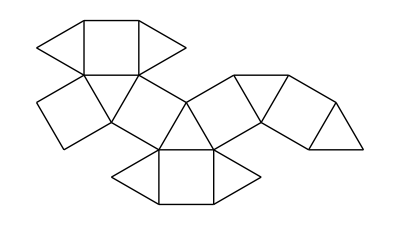
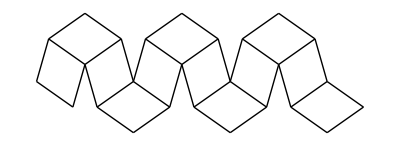
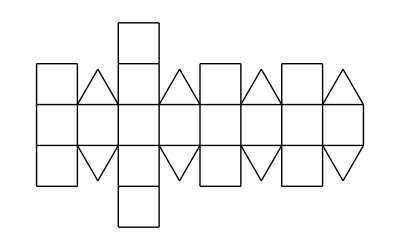
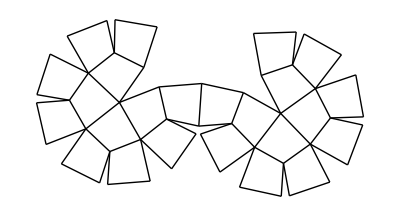
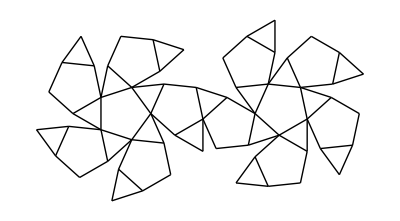
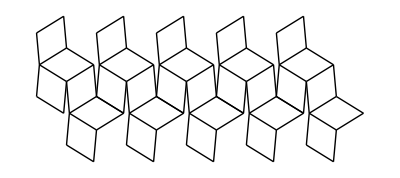
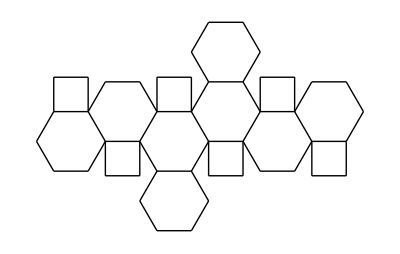
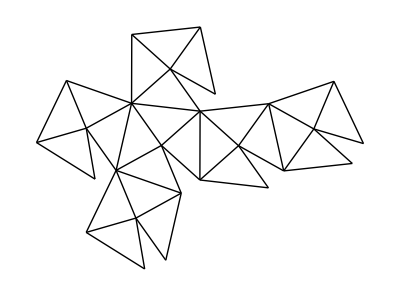
Cuboctahedron | -Graphics3D- | -Graphics- | RhombicDodecahedron | -Graphics3D- | -Graphics-
SmallRhombicuboctahedron | -Graphics3D- | -Graphics- | DeltoidalIcositetrahedron | -Graphics3D- | -Graphics-
Icosidodecahedron | -Graphics3D- | -Graphics- | RhombicTriacontahedron | -Graphics3D- | -Graphics-
TruncatedOctahedron | -Graphics3D- | -Graphics- | TetrakisHexahedron | -Graphics3D- | -Graphics-

Cuboctahedron | RhombicDodecahedron
SmallRhombicuboctahedron | DeltoidalIcositetrahedron
Icosidodecahedron | RhombicTriacontahedron
TruncatedOctahedron | TetrakisHexahedron

```mathematica
Grid[
Map[
{#, PolyhedronData[#],Graphics[PolyhedronData[#, "NetEdges"]],PolyhedronData[#, "Dual"], PolyhedronData[PolyhedronData[#, "Dual"]],Graphics[PolyhedronData[PolyhedronData[#,"Dual"],"NetEdges"]]} &, 
{"Cuboctahedron", "SmallRhombicuboctahedron","Icosidodecahedron","TruncatedOctahedron"}
]
]
Grid[
Map[
{#, PolyhedronData[#, "Dual"]} &, 
{"Cuboctahedron", "SmallRhombicuboctahedron","Icosidodecahedron","TruncatedOctahedron"}
]
]
```